```mathematica
HistoricalPopulationDataUS = {
{1790,3929214},
{1800,5308438},
{1810,7239881},
{1820,9638453},
{1830,12866020},
{1840,17069453},
{1850,23191876},
{1860,31443321},
{1870,38558371},
{1880,50189209},
{1890,62979776},
{1900,76212168},
{1910,92228496},
{1920,106021537},
{1930,123202624},
{1940,132164569},
{1950,151325798},
{1960,179323175},
{1970,203302031},
{1980,226542199},
{1990,248709873},
{2000,281421906},
{2010,308745538}};
```

```mathematica
HistoricalPopulationDataUS//TeXForm
```

\left(
\begin{array}{cc}
 1790 & 3929214 \\
 1800 & 5308438 \\
 1810 & 7239881 \\
 1820 & 9638453 \\
 1830 & 12866020 \\
 1840 & 17069453 \\
 1850 & 23191876 \\
 1860 & 31443321 \\
 1870 & 38558371 \\
 1880 & 50189209 \\
 1890 & 62979776 \\
 1900 & 76212168 \\
 1910 & 92228496 \\
 1920 & 106021537 \\
 1930 & 123202624 \\
 1940 & 132164569 \\
 1950 & 151325798 \\
 1960 & 179323175 \\
 1970 & 203302031 \\
 1980 & 226542199 \\
 1990 & 248709873 \\
 2000 & 281421906 \\
 2010 & 308745538 \\
\end{array}
\right)

```mathematica
DSolve[y'[x] == .027 y[x],y[x],x]
```

{{y[x]→ⅇ^(0.027 x) C[1]}}

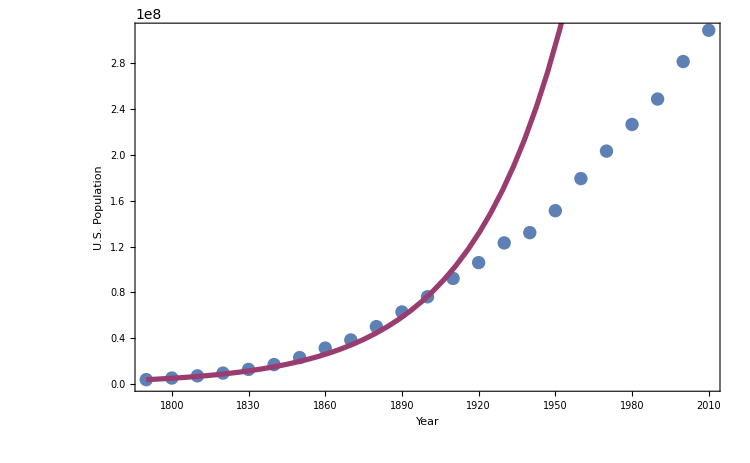

M

```mathematica
Show[ListPlot[HistoricalPopulationDataUS,Frame->True,FrameLabel->{"Year","U.S. Population","U.S. Population Data and Model for k="<>ToString[0.027]},FrameStyle->Directive[FontSize-> 20]],Plot[3929214Exp[0.027 (x-1790)],{x,1790,2010},PlotStyle->{Thickness[0.005],ColorData[1,2]}],ImageSize->750]

M
```

```mathematica
DSolve[{y'[x] == .027 y[x],y[0]==3929214},y[x],x]
```

{{y[x]→3.92921×10^6 ⅇ^(0.027 x)}}

```mathematica
p1[x_]:=3.929214*^6 ⅇ^(0.027 x)
```

```mathematica
HistoricalPopulationDataUS[[1]]
p1[0]
HistoricalPopulationDataUS[[1]][[2]]-p1[0]


HistoricalPopulationDataUS[[2]]
p1[10]
3929214Exp[0.027 (x-1790)]/.x->1800
HistoricalPopulationDataUS[[2]][[2]]-p1[10]


HistoricalPopulationDataUS[[7]]
p1[60]
3929214Exp[0.027 (x-1790)]/.x->1850
HistoricalPopulationDataUS[[7]][[2]]-p1[60]

HistoricalPopulationDataUS[[12]]
p1[110]
3929214Exp[0.027 (x-1790)]/.x->1900
HistoricalPopulationDataUS[[12]][[2]]-p1[110]

HistoricalPopulationDataUS[[17]]
p1[160]
3929214Exp[0.027 (x-1790)]/.x->1950
HistoricalPopulationDataUS[[17]][[2]]-p1[160]
```

{1790,3929214}

3.92921×10^6

0.

{1800,5308438}

5.14713×10^6

5.14713×10^6

161307.

{1850,23191876}

1.98547×10^7

1.98547×10^7

3.3372×10^6

{1900,76212168}

7.65879×10^7

7.65879×10^7

-375755.

{1950,151325798}

2.95432×10^8

2.95432×10^8

-1.44106×10^8

```mathematica
Show[ListPlot[HistoricalPopulationDataUS,Frame->True,FrameLabel->{"Year","U.S. Population","U.S. Population Data and Model for k="<>ToString[0.027]},FrameStyle->Directive[FontSize-> 20]],Plot[3929214Exp[0.027 (x-1790)],{x,1790,2010},PlotStyle->{Thickness[0.005],ColorData[1,2]}],ImageSize->750]
```

-Graphics-

```mathematica
LogisticGrowthUS[t_]:=(3929214 ⅇ^(r (-1790+t)) M)/(-3929214+3929214 ⅇ^(r(-1790+t))+M)
```

```mathematica
LogisticGrowthUS[t_]:=(3929214 ⅇ^(r (-1790+t)) M)/(-3929214+3929214 ⅇ^(r(-1790+t))+M)
ssq=Total[Map[( #1[[2]] -LogisticGrowthUS[ #1[[1]]])^2&,HistoricalPopulationDataUS]];

FindRoot[{D[ssq, r]==0,D[ssq, M]==0},{{r,0.0267},{M,397300000}}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {r,M} = {0.0267,3.973×10^8}. Try perturbing the initial point(s).

{r→0.0267,M→3.973×10^8}

```mathematica
.
```

```mathematica
Log[LogisticGrowthUS[t]]//Simplify
```

Log[(3929214 ⅇ^(r (-1790+t)) M)/(-3929214+3929214 ⅇ^(r (-1790+t))+M)]

```mathematica
f[t_]:= (M P0 ⅇ^(r t))/(P0*(-1+ⅇ^(r t)) + M)
logf[t_]:= Log[M] + Log[P0] + r t - Log[P0(-1+ ⅇ^(r t)) + M]
```

```mathematica
ⅇ^logf[t] - f[t]
```

0

```mathematica
f[0]
f'[t] -( r f[t](1- f[t]/M))//FullSimplify
```

P0

0

```mathematica
DSolve[{y'[t] == r y[t],y[0]==P0},y[t],t]
```

{{y[t]→ⅇ^(r t) P0}}

```mathematica
FindFit[HistoricalPopulationDataUS,LogisticGrowthUS[t]]
```

```mathematica
ssq
```

(-1790 r-Log[M]+Log[3929214 (-1+ⅇ^(1790 r))+M])^2+(-1800 r-Log[3929214]+Log[5308438]-Log[M]+Log[3929214 (-1+ⅇ^(1800 r))+M])^2+(-1810 r-Log[3929214]+Log[7239881]-Log[M]+Log[3929214 (-1+ⅇ^(1810 r))+M])^2+(-1820 r-Log[3929214]+Log[9638453]-Log[M]+Log[3929214 (-1+ⅇ^(1820 r))+M])^2+(-1830 r-Log[3929214]+Log[12866020]-Log[M]+Log[3929214 (-1+ⅇ^(1830 r))+M])^2+(-1840 r-Log[3929214]+Log[17069453]-Log[M]+Log[3929214 (-1+ⅇ^(1840 r))+M])^2+(-1850 r-Log[3929214]+Log[23191876]-Log[M]+Log[3929214 (-1+ⅇ^(1850 r))+M])^2+(-1860 r-Log[3929214]+Log[31443321]-Log[M]+Log[3929214 (-1+ⅇ^(1860 r))+M])^2+(-1870 r-Log[3929214]+Log[38558371]-Log[M]+Log[3929214 (-1+ⅇ^(1870 r))+M])^2+(-1880 r-Log[3929214]+Log[50189209]-Log[M]+Log[3929214 (-1+ⅇ^(1880 r))+M])^2+(-1890 r-Log[3929214]+Log[62979776]-Log[M]+Log[3929214 (-1+ⅇ^(1890 r))+M])^2+(-1900 r-Log[3929214]+Log[76212168]-Log[M]+Log[3929214 (-1+ⅇ^(1900 r))+M])^2+(-1910 r-Log[3929214]+Log[92228496]-Log[M]+Log[3929214 (-1+ⅇ^(1910 r))+M])^2+(-1920 r-Log[3929214]+Log[106021537]-Log[M]+Log[3929214 (-1+ⅇ^(1920 r))+M])^2+(-1930 r-Log[3929214]+Log[123202624]-Log[M]+Log[3929214 (-1+ⅇ^(1930 r))+M])^2+(-1940 r-Log[3929214]+Log[132164569]-Log[M]+Log[3929214 (-1+ⅇ^(1940 r))+M])^2+(-1950 r-Log[3929214]+Log[151325798]-Log[M]+Log[3929214 (-1+ⅇ^(1950 r))+M])^2+(-1960 r-Log[3929214]+Log[179323175]-Log[M]+Log[3929214 (-1+ⅇ^(1960 r))+M])^2+(-1970 r-Log[3929214]+Log[203302031]-Log[M]+Log[3929214 (-1+ⅇ^(1970 r))+M])^2+(-1980 r-Log[3929214]+Log[226542199]-Log[M]+Log[3929214 (-1+ⅇ^(1980 r))+M])^2+(-1990 r-Log[3929214]+Log[248709873]-Log[M]+Log[3929214 (-1+ⅇ^(1990 r))+M])^2+(-2000 r-Log[3929214]+Log[281421906]-Log[M]+Log[3929214 (-1+ⅇ^(2000 r))+M])^2+(-2010 r-Log[3929214]+Log[308745538]-Log[M]+Log[3929214 (-1+ⅇ^(2010 r))+M])^2

```mathematica
NMinimize[{ssq,r>0 , r<1},{r,M}]
```

{1.9328×10^17,{r→5.8111×10^7,M→1.08531×10^8}}

```mathematica
Solve[D[ssq, r]==0,r]
```

$Aborted

```mathematica
FindMinimum[{ssq,r>0},{r,0.0267},{M,397300000}]
```

FindMinimum::sdir: Search direction has become too small.

{1.60572×10^15,{r→0.0267885,M→3.69557×10^8}}

```mathematica
LogisticGrowthUS[t_]:=(3.929214 ⅇ^(r (-1790+t)) M)/(-3.929214+3.929214 ⅇ^(r(-1790+t))+M)
ssq=Total[Map[((#1[[2]])/10^6 -LogisticGrowthUS[ #1[[1]]])^2&,HistoricalPopulationDataUS]];
```

```mathematica
FindMinimum[{ssq,r>0},{r,0.0267},{M,397}]
```

{1605.72,{r→0.0267885,M→369.557}}

```mathematica
SetDirectory[NotebookDirectory[]]
f[t_,r_,M_]:=(3929214 ⅇ^(r (-1790+t)) M)/(-3929214+3929214 ⅇ^(r(-1790+t))+M)
```

/Users/lake/Google Drive/Teaching/Yale/Spring_2017/Math_112/Administration/Homework/Homework #8/Population_Models

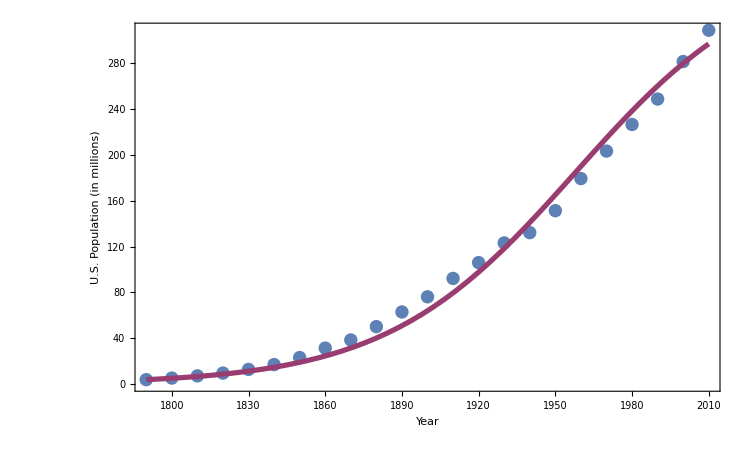

LogisticModel.pdf

```mathematica
Show[ListPlot[Map[{#1[[1]],(#1[[2]])/10^6}&,HistoricalPopulationDataUS],Frame->True,FrameLabel->{"Year","U.S. Population (in millions)","U.S. Population Data and Logistic Model "},FrameStyle->Directive[FontSize-> 20]],Plot[f[x,0.027,369557000]/10^6,{x,1790,2010},PlotStyle->{Thickness[0.005],ColorData[1,2]}],ImageSize->750]
Export["LogisticModel.pdf",%]
```

```mathematica
f[x,0.027,369557000] /. x->t + 1790
```

(1452068538198000 ⅇ^(0.027 t))/(3.69557×10^8+3929214 ⅇ^(0.027 t))

```mathematica
Euler[f0_,x00_?NumericQ,y00_?NumericQ,h0_?NumericQ,xf0_?NumericQ]:=Module[{f=f0,x0=x00,y0=y00,h=h0,xf=xf0,NN,kk,outval={}},
NN=Floor[(xf-x0)/h];
AppendTo[outval,{x0,y0}];
For[kk=1,kk<=NN,kk++,
y0+=h*f[x0,y0];
x0+=h;
AppendTo[outval,{x0,y0}];
];
If[x0<xf,
h = xf-x0;
y0+=h*f[x0,y0];
x0+=h;
AppendTo[outval,{x0,y0}];
];
outval
]
```

```mathematica
Solve[f[x,0.027,369557000] ==369500000,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→2282.96}}

```mathematica
f[1790,0.027,369557000]-HistoricalPopulationDataUS[[1]][[2]]
```

0.

```mathematica
DSolve[{y'[t] == k y[t] + c ,y[0] ==Subscript[P, 0]},y[t],t]//FullSimplify
```

{{y[t]→(-c+ⅇ^(k t) (c+k P_0))/k}}

```mathematica
P[t_]:= c/k(ⅇ^(k t)-1) + P0 ⅇ^(k t)

P[0]
P'[t] - ( k P[t] + c)//FullSimplify
```

P0

0

```mathematica
(ⅇ^(k t)-1) + Subscript[P, 0] ⅇ^(k t)//TeXForm
```

\frac{c \left(e^{k t}-1\right)}{k}+P_0 e^{k t}

```mathematica
.
```

```mathematica
Limit[P[t] /.k->0.027,t->∞]
```

(37.037 c+1. P0) ∞

```mathematica
HistoricalPopulationDataUS[[1]][[2]]
```

3929214

```mathematica
pi[x_]:=3929214 ⅇ^(k (-1790+x))+(c (-1+ⅇ^(k (-1790+x))))/k
```

```mathematica
ssq2=Total[Map[((#1[[2]] -pi[ #1[[1]]])/10^6)^2&,HistoricalPopulationDataUS]]/.Subscript[P, 0]->HistoricalPopulationDataUS[[1]][[2]]//ExpandAll;
FindMinimum[{ssq2,k>0},{k,0.0267},{c,100}]
```

{796.79,{k→0.0109445,c→296684.}}

```mathematica
Solve[0==1.9703693963538944+6.855444889876064*^-7 a]
```

{{a→-2.87417×10^6}}

```mathematica
c/k(ⅇ^(k t)-1) + Subscript[P, 0] ⅇ^(k t) /.t-> x-1790 /. Subscript[P, 0]-> HistoricalPopulationDataUS[[1]][[2]]
```

3929214 ⅇ^(k (-1790+x))+(c (-1+ⅇ^(k (-1790+x))))/k

```mathematica
Manipulate[Show[ListPlot[HistoricalPopulationDataUS,Frame->True,FrameLabel->{"Year","U.S. Population","U.S. Population Data and Model for k="<>ToString[k]<>" c="<>ToString[c]},FrameStyle->Directive[FontSize-> 20]],Plot[3929214 ⅇ^(k (-1790+x))+(c (-1+ⅇ^(k (-1790+x))))/k,{x,1790,2010},PlotStyle->{Thickness[0.005],ColorData[1,2]}],ImageSize->750],{k,.01,.04},{c,0,10^6},LabelStyle-> Directive[FontSize->20]]
```

/Users/lake/Google Drive/Teaching/Yale/Spring_2017/Math_112/Administration/Homework/Homework #8/Population_Models

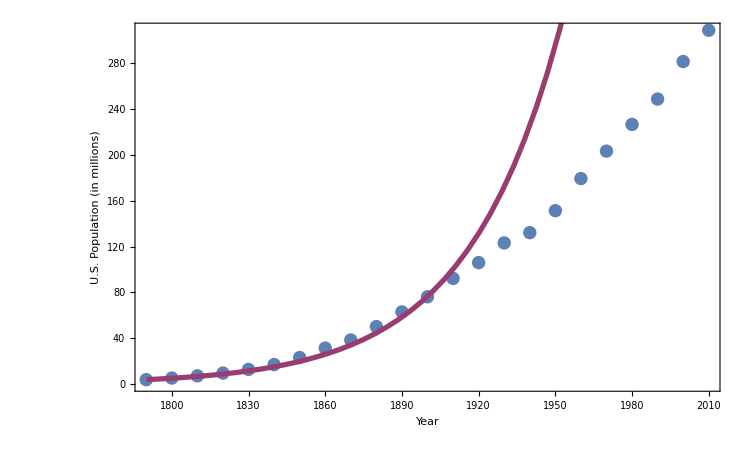

exponentialmodel.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
Show[ListPlot[Map[{#1[[1]],(#1[[2]])/10^6}&,HistoricalPopulationDataUS],Frame->True,FrameLabel->{"Year","U.S. Population (in millions)","U.S. Population Data and Exponential Model for k="<>ToString[0.027]},FrameStyle->Directive[FontSize-> 20]],Plot[3.929214Exp[0.027 (x-1790)],{x,1790,2010},PlotStyle->{Thickness[0.005],ColorData[1,2]}],ImageSize->750]
Export["exponentialmodel.pdf",%]
```

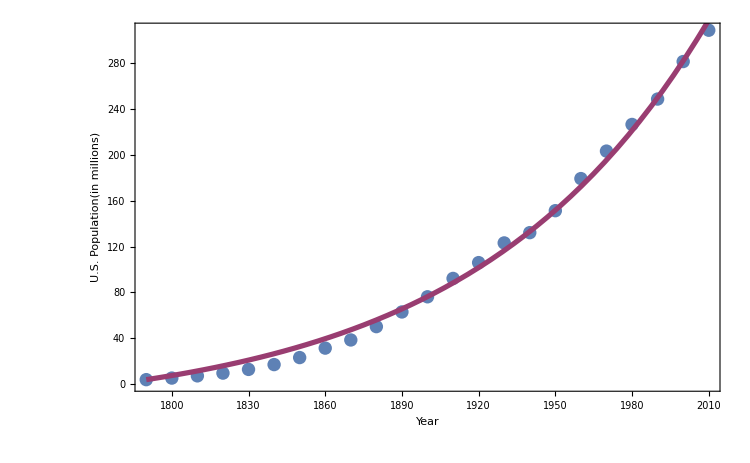

immigrationmodel.pdf

```mathematica
Show[ListPlot[Map[{#1[[1]],(#1[[2]])/10^6}&,HistoricalPopulationDataUS],Frame->True,FrameLabel->{"Year","U.S. Population(in millions)","U.S. Population Data and Model #2 for k="<>ToString[.011]<>" c="<>ToString[296684]},FrameStyle->Directive[FontSize-> 20]],Plot[(3929214 ⅇ^(k (-1790+x))+(c (-1+ⅇ^(k (-1790+x))))/k)/10^6/.{k->0.010944518654638502,c->296683.5577579119},{x,1790,2010},PlotStyle->{Thickness[0.005],ColorData[1,2]}],ImageSize->750]
Export["immigrationmodel.pdf",%]
```